## Built-in classifiers

```mathematica
cl=Classify["CountryFlag"]
```

ClassifierFunction[…]


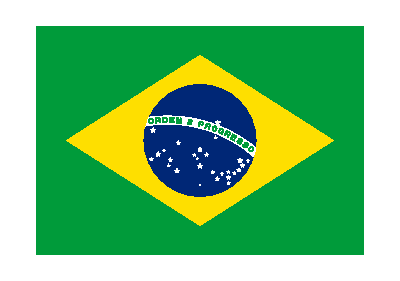
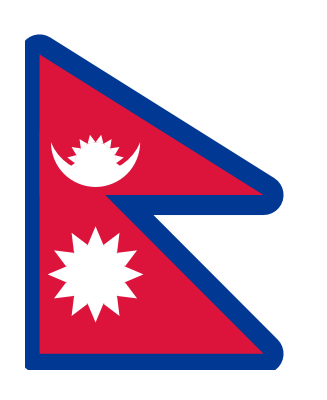
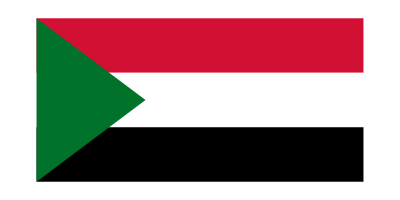

```mathematica
flags=CountryData[#,"Flag"]&/@{"France", "Brazil","Nepal","Sudan"}
```

```mathematica
cl[flags,"TopProbabilities"]
```

{{France→0.909483},{Brazil→0.909483},{Nepal→0.909483},{Sudan→0.909483}}

```mathematica
Information[cf,"Classes"]
```

Missing[UnknownProperty,Classes]

```mathematica
Information[cf]
```

## Creating classifiers

```mathematica
mnistTrain=ResourceData["MNIST","TrainingData"];
mnistTest=ResourceData["MNIST","TestData"];
```

```mathematica
mnistTrainSample=RandomSample[mnistTrain,10000];
```

```mathematica
mnistCl=Classify[mnistTrain]
```

ClassifierFunction[…]

```mathematica
mnistCl1=Classify[mnistTrainSample,Method->"NearestNeighbors"]
```

ClassifierFunction[…]

```mathematica
mnistCl2=Classify[mnistTrainSample,Method->"LogisticRegression"]
```

ClassifierFunction[…]

```mathematica
Information[{mnistCl1,mnistCl2}]
```

{Classifier information
Data type | Image
Number of classes | 10
Method | NearestNeighbors
Single evaluation time | 76.8 ms/example
Batch evaluation speed | 763. examples/s
Model memory | 62.9 MB
Training examples used | 10000 examples
Training time | 1.75 s,Classifier information
Data type | Image
Number of classes | 10
Accuracy | (88.81.0) %
Method | LogisticRegression
Single evaluation time | 4.15 ms/example
Batch evaluation speed | 8.13 examples/ms
Loss | 0.379 ± 0.033
Model memory | 387. kB
Training examples used | 10000 examples
Training time | 43. s
 | }

```mathematica
confusionMatrix=ClassifierMeasurements[mnistCl,mnistTest,"ConfusionMatrixPlot"];
```

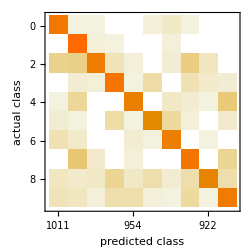

```mathematica
Show[confusionMatrix,ImageSize->250]
```

```mathematica
Export[NotebookDirectory[]<>"pics/08-confusion-matrix-plot.pdf",%]
```

/home/jam/Kuweta/mma_lessons/code/pics/08-confusion-matrix-plot.pdf

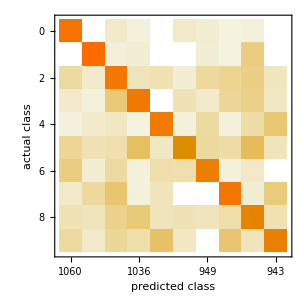
Classifier Measurements
Classifier method | LogisticRegression
Number of test examples | 10000
Accuracy | (89.220.31) %
Accuracy baseline | (11.350.32) %
Geometric mean of probabilities | 0.691 ± 0.0068
Mean cross entropy | 0.37 ± 0.0099
Single evaluation time | 4.7 ms/example
Batch evaluation speed | 28. examples/ms
-Graphics- |

```mathematica
ClassifierMeasurements[mnistCl2,mnistTest]
```